## Fundamental Solution

```mathematica
DSolve[f''[x]-1/x f'[x]==-x^2(ⅇ^(-mD x) mD^2 π)/(2 x),f[x],x]
```

{{f[x]→1/2 ⅇ^(-mD x) mD π (-1/mD^2-x/mD)+1/2 x^2 C[1]+C[2]}}

```mathematica
DSolve[f''[x]-1/x f'[x]-x^3 f[x]==0,f[x],x]
```

{{f[x]→(x BesselI[-2/5,(2 x^(5/2))/5] C[1] Gamma[3/5])/5^(2/5)+(-1/5)^(2/5) x BesselI[2/5,(2 x^(5/2))/5] C[2] Gamma[7/5]}}

```mathematica
DSolve[f''[x]-1/x f'[x]-x^3 A f[x]==0,f[x],x]
```

{{f[x]→(A^(1/5) x BesselI[-2/5,2/5 √A x^(5/2)] C[1] Gamma[3/5])/5^(2/5)+((-1)^(2/5) A^(1/5) x BesselI[2/5,2/5 √A x^(5/2)] C[2] Gamma[7/5])/5^(2/5)}}

```mathematica
DSolve[f''[x]-1/x f'[x]-x^3 A f[x]==-4π d x^3 DiracDelta[x],f[x],x]
```

{{f[x]→(A^(1/5) x BesselI[-2/5,2/5 √A x^(5/2)] C[1] Gamma[3/5])/5^(2/5)+((-1)^(2/5) A^(1/5) x BesselI[2/5,2/5 √A x^(5/2)] C[2] Gamma[7/5])/5^(2/5)}}

```mathematica
u1[x_,a_]:=x  BesselI[-2/5,2/5 x^(5/2) √a] ;
```

```mathematica
D[u1[x,a],{x,2}]-1/x D[u1[x,a],x]-x^3 a u1[x,a]//FullSimplify
```

0

```mathematica
u2[x_,a_]:=x BesselI[2/5,(2 x^(5/2))/5 √a];
```

```mathematica
D[u2[x,a],{x,2}]-1/x D[u2[x,a],x]-x^3 a u2[x,a]//FullSimplify
```

0

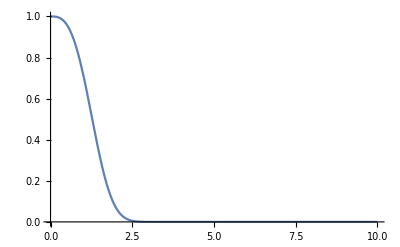

```mathematica
Plot[u1[x]-u2[x],{x,0,10},PlotRange->All]
```

```mathematica
u1[x,mu]-u2[x,mu]//FullSimplify
```

(√(1/2 (5+√5)) x BesselK[2/5,2/5 √mu x^(5/2)])/π

```mathematica
Reu[x_,a_]:=x BesselK[2/5,2/5 √a x^(5/2)];
```

```mathematica
D[Reu[x,a],{x,2}]-1/x D[Reu[x,a],x]-x^3 a Reu[x,a]//FullSimplify
```

0

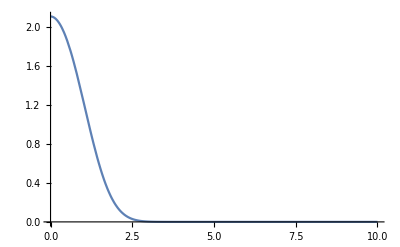

```mathematica
Plot[Reu[x,1],{x,0,10},PlotRange->All]
```

```mathematica
Limit[Reu[x,a],x->0]//FullSimplify
```

(5^(2/5) Gamma[2/5])/(2 a^(1/5))

## Homogeneous Solution with BCs

### BC1 : y'[0] = y[0]=0

```mathematica
D[u1[x],x]
```

BesselI[-2/5,(2 x^(5/2))/5]+1/2 x^(5/2) (BesselI[-7/5,(2 x^(5/2))/5]+BesselI[3/5,(2 x^(5/2))/5])

```mathematica
Limit[D[u1[x],x],x->0]
```

0

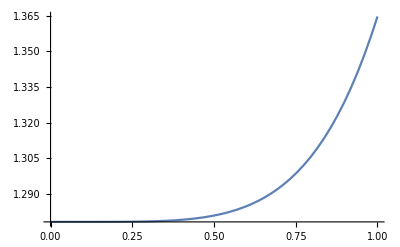

```mathematica
Plot[u1[x],{x,0,1},PlotRange->All]
```

```mathematica
Limit[u1[x],x->0]
```

5^(2/5)/Gamma[3/5]

```mathematica
D[u2[x],x]
```

BesselI[2/5,(2 x^(5/2))/5]+1/2 x^(5/2) (BesselI[-3/5,(2 x^(5/2))/5]+BesselI[7/5,(2 x^(5/2))/5])

```mathematica
Limit[D[u2[x],x],x->0]
```

0

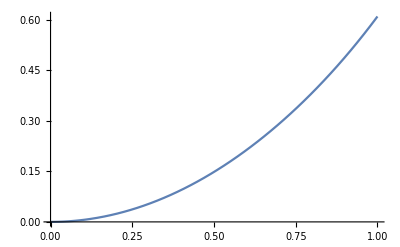

```mathematica
Plot[u2[x],{x,0,1}]
```

```mathematica
u2[0]
```

0

```mathematica
y1[x_]:=u2[x];
```

### BC2 : y'[∞] = 0

```mathematica
Limit[D[u1[x]-u2[x],x],x->∞]
```

0

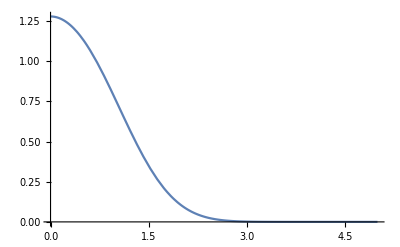

```mathematica
Plot[u1[x]-u2[x],{x,0,5},PlotRange->All]
```

```mathematica
y2[x_]:=u1[x]-u2[x];
```

## Construction of Wronskian

```mathematica
D[y2[x],x]y1[x]-y2[x]D[y1[x],x]//FullSimplify
```

-(5 √(1/2 (5+√5)) x)/(2 π)

```mathematica
W[x_]:=-(5 √(1/2 (5+√5)) x)/(2 π);
```

```mathematica
c=N[(5 √(1/2 (5+√5)))/(2 π)]
```

1.51365

## Construction of Inhomogeneous Solution

```mathematica
y[x_?NumericQ]:=-1/c y2[x]NIntegrate[y1[s]g2Inter[s],{s,10^-9,x},MinRecursion->20,MaxRecursion->50,WorkingPrecision->30,PrecisionGoal->10]-1/c y1[x]NIntegrate[y2[s]g2Inter[s],{s,x,∞},MaxRecursion->50,WorkingPrecision->30,PrecisionGoal->10];
```

```mathematica
y[6]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.

```mathematica
yTab=Table[{i,0},{i,0.1,6,0.1}];
SetSharedVariable[yTab];
```

```mathematica
ParallelDo[yTab[[i,2]]=y[yTab[[i,1]]],{i,1,Length[yTab]}]
```

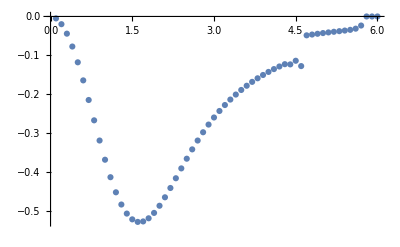

```mathematica
ListPlot[yTab]
```

```mathematica
yTab[[-15]]
```

{4.6,-0.292476}

```mathematica
yInter=Interpolation[yTab[[;;-15]]];
```

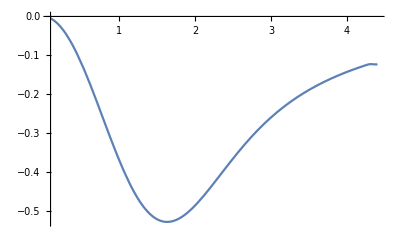

```mathematica
Plot[yInter[x],{x,0.1,4.4}]
```

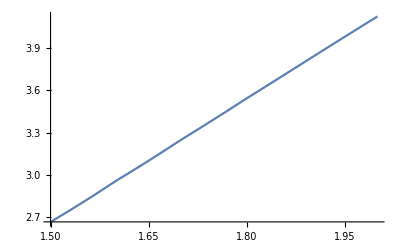

```mathematica
Plot[yInter''[x]-1/x yInter'[x]-x^3 yInter[x],{x,1.5,2}]
```

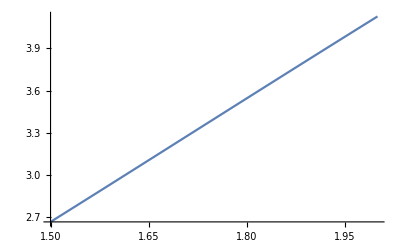

```mathematica
Plot[x^3 g[x],{x,1.5,2}]
```

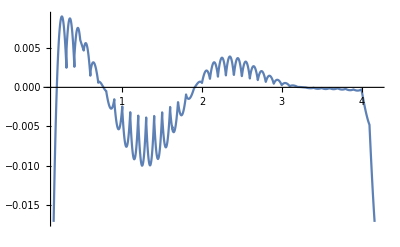

```mathematica
Plot[(yInter''[x]-1/x yInter'[x]-x^3 yInter[x])-(x^3 g[x]),{x,0.1,4.2}]
```